# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at xh=1. Initial condition is a wide distribution which narrows on approach to the fixed point.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP=λ*D[xh*P[x, xh], x]+D[xh*P[x, xh], xh]-κ*D[x*P[x, xh],xh]+λ*D[P[ x, xh],{x,2}]+D[P[x, xh],{xh,2}]
```

P[x,xh]+xh P^(0,1)[x,xh]-x κ P^(0,1)[x,xh]+P^(0,2)[x,xh]+xh λ P^(1,0)[x,xh]+λ P^(2,0)[x,xh]

## Choose the parameter values

```mathematica
λs = {0.05, 0.1, 0.2,0.5, 1};
κs = {0.1, 0.2, 0.5,1, 2};
params = Flatten[Table[{λ->l, κ->k}, {l, λs}, {k, κs}], 1]
legend =  Flatten[Table["λ="<>ToString[l]<>"; "<> "κ="<>ToString[k], {l, λs},{k, κs}], 1];
```

{{λ→0.05,κ→0.1},{λ→0.05,κ→0.2},{λ→0.05,κ→0.5},{λ→0.05,κ→1},{λ→0.05,κ→2},{λ→0.1,κ→0.1},{λ→0.1,κ→0.2},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.1,κ→2},{λ→0.2,κ→0.1},{λ→0.2,κ→0.2},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.2,κ→2},{λ→0.5,κ→0.1},{λ→0.5,κ→0.2},{λ→0.5,κ→0.5},{λ→0.5,κ→1},{λ→0.5,κ→2},{λ→1,κ→0.1},{λ→1,κ→0.2},{λ→1,κ→0.5},{λ→1,κ→1},{λ→1,κ→2}}

## Set up the mesh, boundary conditions, and initial condition

#### Choose the same initial width for every parameter set: the one with the largest s.s. width in x

```mathematica
Table[1/(2κ)+((1+κ) λ)/(2κ)/.p, {p, params}]
```

{5.275,2.65,1.075,0.55,0.2875,5.55,2.8,1.15,0.6,0.325,6.1,3.1,1.3,0.7,0.4,7.75,4.,1.75,1.,0.625,10.5,5.5,2.5,3/2,1}

```mathematica
{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[21]]
```

{{10.5,1/2},{1/2,0.55}}

#### Boundary condition at x*=1, y* = 2k/(1+Sqrt(1-4*l*k))

#### Also choose initial width for the steady-state width of each parameter pair

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
ystars = Table[Re[2*κ/(1+Sqrt[1-4*κ*λ])]/.p, {p, params}]
```

{0.100505,0.202041,0.513167,1.05573,2.25403,0.101021,0.204168,0.527864,1.12702,2.76393,0.102084,0.208712,0.563508,1.38197,2.5,0.105573,0.225403,1.,1.,1.,0.112702,0.276393,0.5,1/2,1/2}

```mathematica
xf=20;
icPos = {5,5}
icVar = {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[21]] 
(*ic0 = N[Table[PDF[MultinormalDistribution[{5,5},icVar], {x, xh}], {i, icPos}]];*)
ic0 = N[Table[PDF[MultinormalDistribution[icPos,icVar], {x, xh}], {i, params}]];(*ic0 : Choose widest s.s. distribution of the parameter values*)
(*icSS = N[Table[PDF[MultinormalDistribution[icPos,{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.p], {x, xh}], {p, params}]];*)
(*icSS : Choose s.s. distribution width for each of the parameter values*)
bcs = Table[{P[-xf, xh]==0,
           P[xf, xh]==0,
           P[x, xf]==0,
           P[x, ystar]==0
}, {ystar,ystars}]
meshes=Table[ToElementMesh[Rectangle[{-xf, ystar}, {xf, xf}],MaxCellMeasure->0.025], {ystar, ystars}]
```

{5,5}

{{10.5,1/2},{1/2,0.55}}

{{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.100505]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.202041]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.513167]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1.05573]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,2.25403]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.101021]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.204168]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.527864]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1.12702]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,2.76393]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.102084]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.208712]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.563508]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1.38197]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,2.5]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.105573]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.225403]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1.]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1.]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1.]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.112702]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.276393]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,0.5]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1/2]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1/2]==0}}

{ElementMesh[{{-20.,20.},{0.100505,20.}},{QuadElement[<31878>]}],ElementMesh[{{-20.,20.},{0.202041,20.}},{QuadElement[<31878>]}],ElementMesh[{{-20.,20.},{0.513167,20.}},{QuadElement[<31372>]}],ElementMesh[{{-20.,20.},{1.05573,20.}},{QuadElement[<30360>]}],ElementMesh[{{-20.,20.},{2.25403,20.}},{QuadElement[<28589>]}],ElementMesh[{{-20.,20.},{0.101021,20.}},{QuadElement[<31878>]}],ElementMesh[{{-20.,20.},{0.204168,20.}},{QuadElement[<31878>]}],ElementMesh[{{-20.,20.},{0.527864,20.}},{QuadElement[<31372>]}],ElementMesh[{{-20.,20.},{1.12702,20.}},{QuadElement[<30360>]}],ElementMesh[{{-20.,20.},{2.76393,20.}},{QuadElement[<27830>]}],ElementMesh[{{-20.,20.},{0.102084,20.}},{QuadElement[<31878>]}],ElementMesh[{{-20.,20.},{0.208712,20.}},{QuadElement[<31878>]}],ElementMesh[{{-20.,20.},{0.563508,20.}},{QuadElement[<31119>]}],ElementMesh[{{-20.,20.},{1.38197,20.}},{QuadElement[<29854>]}],ElementMesh[{{-20.,20.},{2.5,20.}},{QuadElement[<28083>]}],ElementMesh[{{-20.,20.},{0.105573,20.}},{QuadElement[<31878>]}],ElementMesh[{{-20.,20.},{0.225403,20.}},{QuadElement[<31878>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{0.112702,20.}},{QuadElement[<31878>]}],ElementMesh[{{-20.,20.},{0.276393,20.}},{QuadElement[<31625>]}],ElementMesh[{{-20.,20.},{0.5,20.}},{QuadElement[<31372>]}],ElementMesh[{{-20.,20.},{0.5,20.}},{QuadElement[<31372>]}],ElementMesh[{{-20.,20.},{0.5,20.}},{QuadElement[<31372>]}]}

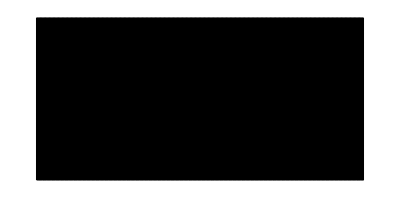

```mathematica
meshes[[1]]["Wireframe"]
```

## Calculate the probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, mesh_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,Element[{x, xh}, mesh], 
Method->"FiniteElement"];
Return[(P/.N[[1]])];
]
```

```mathematica
(*solsSS=MapThread[NDSolverParams, {params, icSS, bcs, meshes}];*)
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, meshes}];
```

```mathematica
(*fluxSS = Table[Derivative[0,1][sol],{sol, solsSS}];*)
fluxIc0 = Table[Derivative[0,1][sol],{sol, solsIc0}];
```

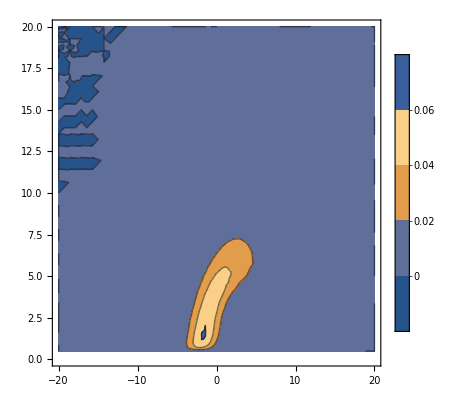

```mathematica
(*cSS =ContourPlot[solsSS[[1]][x, xh], {x, -xf, xf}, {xh, 0, xf}, PlotLegends->Automatic, PlotRange->{-0.01, 0.01}];*)
cIc0 =ContourPlot[solsIc0[[25]][x, xh], {x, -xf, xf}, {xh, 0, xf}, PlotLegends->Automatic, PlotRange->{-0.01, 0.1}];
(*Show[cSS]*)
Show[cIc0]
```

```mathematica
XIc0 =MapThread[#1[x,#2]&,{fluxIc0,ystars}];
```

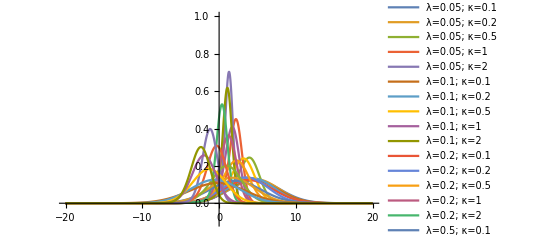

```mathematica
Plot[XIc0, {x, -xf, xf}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

```mathematica
(*normsSS = Table[NIntegrate[xp, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
meansSS= Table[NIntegrate[xp*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
secondSS = Table[NIntegrate[xp*x*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}];
varsSS= secondSS-meansSS^2
diffSS = varsSS/meansSS;*)
```

Table::iterb: Iterator {xp,XSS} does not have appropriate bounds.

Table[NIntegrate[xp,{x,-10,15},WorkingPrecision→10],{xp,XSS}]

Table::iterb: Iterator {xp,XSS} does not have appropriate bounds.

Table[NIntegrate[xp x,{x,-10,15},WorkingPrecision→10],{xp,XSS}]

Table::iterb: Iterator {xp,XSS} does not have appropriate bounds.

Table[NIntegrate[xp x x,{x,-10,15},WorkingPrecision→10],{xp,XSS}]-Table[NIntegrate[xp x,{x,-10,15},WorkingPrecision→10],{xp,XSS}]^2

```mathematica
normsIc0 = Table[NIntegrate[xp, {x, -10, 15}, WorkingPrecision->10], {xp, XIc0}]
meansIc0= Table[NIntegrate[xp*x, {x, -10, 15}, WorkingPrecision->10], {xp, XIc0}]
secondIc0 = Table[NIntegrate[xp*x*x, {x, -10, 15}, WorkingPrecision->10], {xp, XIc0}];
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0;
```

{1.003211368,1.002561736,0.9997249228,0.9998697952,0.9699131837,1.003442236,1.002853417,1.001041707,1.001001375,0.983484105,1.003682483,1.003172877,1.002051673,1.000678543,0.9888813454,1.003722095,1.003353484,1.001167449,0.9968641732,0.9786438569,0.9984918788,1.001312702,0.998812794,0.9890576188,0.9559754723}

{4.686368565,4.52040662,3.226478255,1.873278012,1.063883023,4.377646437,4.108847281,2.698482823,1.477641563,0.9134206734,3.781342595,3.391626244,1.979171367,1.03259746,0.2852780326,2.137036327,1.665748428,0.8687496203,-0.3965461938,-1.2297733,-0.2114146504,-0.5299390308,-1.321438313,-1.982803302,-2.371110478}

{10.2436514,9.29040088,3.98528455,1.55462029,0.780749843,10.2034439,8.78507787,3.67080671,1.52388867,0.80652841,10.2652685,8.37519252,3.5899681,1.62475927,0.782817563,11.1456961,8.61093522,4.20391378,1.81788082,1.04134793,13.1296056,9.9665839,4.77191253,2.42946488,1.8377325}

```mathematica
grid = Flatten[Table[{l, s}, {l, λs}, {s, κs}], 1];
params
```

{{λ→0.05,κ→0.1},{λ→0.05,κ→0.2},{λ→0.05,κ→0.5},{λ→0.05,κ→1},{λ→0.05,κ→2},{λ→0.1,κ→0.1},{λ→0.1,κ→0.2},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.1,κ→2},{λ→0.2,κ→0.1},{λ→0.2,κ→0.2},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.2,κ→2},{λ→0.5,κ→0.1},{λ→0.5,κ→0.2},{λ→0.5,κ→0.5},{λ→0.5,κ→1},{λ→0.5,κ→2},{λ→1,κ→0.1},{λ→1,κ→0.2},{λ→1,κ→0.5},{λ→1,κ→1},{λ→1,κ→2}}

```mathematica
(*normArraySS = ArrayReshape[normsSS, {5, 5}];
varArraySS = ArrayReshape[varsSS, {5, 5}];
meanArraySS = ArrayReshape[meansSS, {5, 5}];
diffArraySS = ArrayReshape[diffSS, {5, 5}];*)
normArrayIc0 = ArrayReshape[normsIc0, {5,5}];
varArrayIc0 = ArrayReshape[varsIc0, {5, 5}];
meanArrayIc0 = ArrayReshape[meansIc0, {5, 5}];
diffArrayIc0 = ArrayReshape[diffIc0, {5, 5}];
```

```mathematica
cf[x_]:=Blend[{{-2, Red},{ 1,White},{5,Blue}}, x]
```

```mathematica
xticks = Transpose[{{1, 2, 3, 4, 5}, λs}];
yticks = Transpose[{{1, 2, 3, 4, 5}, κs}];
```

```mathematica
ArrayPlot[varArraySS, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArraySS]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[normArraySS, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"norm(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

ArrayPlot::mat: Argument varArraySS at position 1 is not a list of lists.

ArrayPlot[varArraySS,ColorFunction→(Blend[{{-1,Red},{0,White},{1,Blue}},#1]&),PlotLegends→{Placed[BarLegend[Automatic,None,LegendLabel→var(x)],Right]},FrameTicks→{{{1,0.05},{2,0.1},{3,0.2},{4,0.5},{5,1}},{{1,0.1},{2,0.2},{3,0.5},{4,1},{5,2}}},DataReversed→True,FrameLabel→{λ,κ}]

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[meanArraySS].

Table::iterb: Iterator {i,Flatten[meanArraySS]} does not have appropriate bounds.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Blend[{{-2,Red},{0,White},{5,Blue}},i],{i,Flatten[meanArraySS]}],{5,5}].

ArrayPlot::mat: Argument ArrayReshape[Table[Blend[{{-2,Red},{0,White},{5,Blue}},i],{i,Flatten[meanArraySS]}],{5,5}] at position 1 is not a list of lists.

ArrayPlot[ArrayReshape[Table[Blend[{{-2,Red},{0,White},{5,Blue}},i],{i,Flatten[meanArraySS]}],{5,5}],PlotLegends→{Placed[,Right]},FrameTicks→{{{1,0.05},{2,0.1},{3,0.2},{4,0.5},{5,1}},{{1,0.1},{2,0.2},{3,0.5},{4,1},{5,2}}},DataReversed→True,FrameLabel→{λ,κ}]

ArrayPlot::mat: Argument normArraySS at position 1 is not a list of lists.

ArrayPlot[normArraySS,ColorFunction→(Blend[{White,Blue},#1]&),PlotLegends→{Placed[BarLegend[Automatic,Automatic,LegendLabel→norm(e(x))],Right]},FrameTicks→{{{1,0.05},{2,0.1},{3,0.2},{4,0.5},{5,1}},{{1,0.1},{2,0.2},{3,0.5},{4,1},{5,2}}},DataReversed→True,FrameLabel→{λ,κ}]

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[normArrayIc0, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"norm(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-